## 2. DOMAčA NALOGA!!!

# 1. NALOGA

V Mathematici predstavimo daljico v obliki Daljica [AA_, BB_], kjer sta AA in BB tocki predstavljeni s parom koordinat v obliki {x, y}. 

Sestavi naslednje funkcije:

```mathematica
d = Daljica [{-1, 1}, {3, -1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
d2 = Daljica[{-1, -1}, {3, 1}]
```

Daljica[{-1,-1},{3,1}]

```mathematica
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,2},{3,0}]

Dolžina daljice:

```mathematica
Dolzina [Daljica[AA_, BB_]] := Norm[BB - AA]
```

```mathematica
Dolzina[d]
```

2 √5

Slika:

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
```

Nariši:

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
```

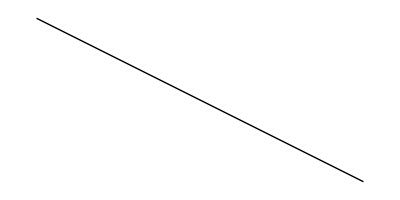

```mathematica
Narisi[d]
```

```mathematica
ClearAll[x, y]
```

Enačba nosilke:

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, x2, y1, y2, k, n},
{x1, y1} = AA;
{x2, y2} = BB;

k = (y2 - y1)/ (x2 - x1);
n = n /. First[Solve[y1 == k*x1 + n, n]];
y == k * x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

# 2. NALOGA

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0,  r ≤ 1, s ≥ 0,  s ≤ 1}, {r, s}];
If[resitev == {}, 
{},
First [AA + r (BB - AA) /. resitev ]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

# 3. NALOGA

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik. Primer m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}].

```mathematica
m1=Mnogokotnik[{0,0}, {1, 1}, {0,3}, {-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
m2=Mnogokotnik[{1, 3}, {0, 2}, {2, 2}, {-1, 0}]
```

Mnogokotnik[{1,3},{0,2},{2,2},{-1,0}]

Slika [Mnogokotnik[t_ _]]:

```mathematica
Stranice[{AA_, BB_, CC_, DD_}] := {{AA, BB}, {BB, CC}, {CC, DD}, {AA, DD}}
```

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
m1 = Append[m1, First[m1]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

Narisi [m__Mnogokotnik]:

```mathematica
Narisi[m__Mnogokotnik]:= Graphics[Map[Slika, List[m]]]
```

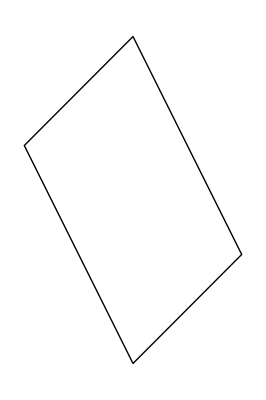

```mathematica
Narisi[m1]
```

PravilniNKotnik [n_, r_]:

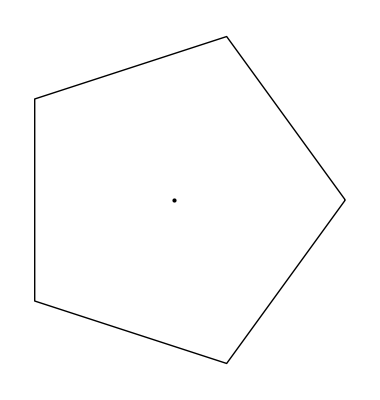

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2]
```

PravilniNKotnik [n_, r_, phi_]

```mathematica
PravilniNKotnik[n_, r_, phi_]:= Manipulate[Graphics[
{Line[Table[{r*Cos[(2Pi*i + x)/n],r*Sin[(2Pi*i + x)/n]},{i,0,n}]],Point[{0,0}]}], {x, 0, Pi}]
```

```mathematica
PravilniNKotnik[5, 2, Pi]
```

Daljice [Mnogokotnik[t__]]

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t}, {2, 2}, 1]
```

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Daljice[m1]
```

{{{{0,0},{1,1}}},{{{1,1},{0,3}}},{{{0,3},{-1,2}}},{{{-1,2},{0,0}}}}

# 4. NALOGA

Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in daljice. Pri tem uporabi že napisane funkcije ter pazi, da rezultat ne istih presečišč večkrat. Poskusi uporabiti vgrajeni funkciji Select in DeleteDuplicates. Pomagaj si z naslednjimi primeri. Funkcijo lahko deﬁniramo tudi na naslednji način (namesto argumenta damo znak #, na koncu deﬁnicije pa dodamo znak &.

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

```mathematica
?DeleteDuplicates
```

DeleteDuplicates[list] deletes all duplicates from list.
DeleteDuplicates[list,test] applies test to pairs of elements to determine whether they should be considered duplicates.

Presek[m_Mnogokotnik, d_Daljica]

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0,  r ≤ 1, s ≥ 0,  s ≤ 1}, {r, s}];
If[resitev == {}, 
{},
First [AA + r (BB - AA) /. resitev ]
]
]
```

```mathematica
d1 = Daljica[{-1,1},{3,-1}];
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
m = Append[m1, m1[[1]]]
seznamDaljic = Map[Daljica, Daljice[m]]
Daljice[Mnogokotnik[t__]] := Partition[{t},2,1]
Daljice[m]
Daljice1 = Partition[Flatten[Daljice[m]], 2, 2]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

{{0,0},{1,1},{1,1},{0,3},{0,3},{-1,2},{-1,2},{0,0}}

```mathematica
PresekBrezSeznama = Presek1[m__Mnogokotnik, d__Daljica] :=  
	For[i = 1, i <= Length[Daljice[m]], i++, Print[Presek[Daljica[Daljice[m][[i]][[1]], Daljice[m][[i]][[2]]], d]]]
```

```mathematica
Presek1[m, d1]
```

{1/3,1/3}

{}

{}

{-1/3,2/3}

# 5. NALOGA

Spodnja funkcija izračuna (uporabi) funkcijo f na vseh parih iz dveh seznamov.

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
VsiPari[k,{2,3,4},{7,3,5}]
```

{k[2,7],k[2,3],k[2,5],k[3,7],k[3,3],k[3,5],k[4,7],k[4,3],k[4,5]}

```mathematica
VsiPari[f,{{1,2},{3,4}},{{aa,bb},{dd,cc}}]
```

{{{f[1,aa],f[1,bb]},{f[1,dd],f[1,cc]}},{{f[2,aa],f[2,bb]},{f[2,dd],f[2,cc]}},{{f[3,aa],f[3,bb]},{f[3,dd],f[3,cc]}},{{f[4,aa],f[4,bb]},{f[4,dd],f[4,cc]}}}

```mathematica
Outer[f,{2,4,3,{5},9}]
```

{f[2],f[4],f[3],{f[5]},f[9]}

```mathematica
Flatten[Outer[f,{2,4,3,{5},9}],1]
```

{f[2],f[4],f[3],f[5],f[9]}

Preuči, kaj točno naredita funkciji Outer in Flatten. Poglej v pomoč in preizkusi na primerih.

Outer: skupaj združi sezname ter jih razporedi po vseh možnih načinih (jih lahko tudi vgnezdi).
Flatten: vgnezdene zanke odgnezdi, glede na dano število

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0,  r ≤ 1, s ≥ 0,  s ≤ 1}, {r, s}];
If[resitev == {}, 
{},
First [AA + r (BB - AA) /. resitev ]
]
]
```

Presek [m1_Mnogokotnik, m2_Mnogokotnik]:

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:=
For[j = 1, j ≤Length[Daljice[m2]], j++, 
For[i=1, i<Length[Daljice[m1]], i++,
Print[Presek[Daljica[Daljice[m1][[i]][[1]], Daljice[m1][[i]][[2]]],
 Daljica[Daljice[m2][[i]][[1]], Daljice[m2][[i]][[2]]]]]]]
```

```mathematica
Presek[m1, m2]
```

{}

{1/2,2}

{}

{1/2,2}

{}

{1/2,2}

# 6. NALOGA

VEKTORSKI PRODUKT

Določi vektorje:

```mathematica
AA:={8, 3, -4}
BB := {1, 0, 6}
CC := {9, 3, 7}
vektor1 [AA_, BB_]:= BB - AA
vektor2[AA_, CC_]:=CC-AA
```

```mathematica
V1 = vektor1[AA, BB]
V2 =vektor2[BB, CC]
```

{-7,-3,10}

{8,3,1}

```mathematica
V3 =Cross[V1, V2]
```

{-33,87,3}

```mathematica
V123 = {{V1},{V2},{V3}}
```

{{{-7,-3,10}},{{8,3,1}},{{-33,87,3}}}

Nariši:

```mathematica
Graphics3D[Map[Line, V123]]
```

-Graphics3D-